# Monkeypox Parameter Optimization

## Initializing Data

```mathematica
Import["/Users/wagner.palacio/Documents/Projeto/Repos/SystemModeling/Projects/Monkeypox/SEIQREpidemiologyModel.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/Projects/Coronavirus-propagation-dynamics/WL/EpidemiologyModelModifications.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/Projects/Coronavirus-propagation-dynamics/WL/EpidemiologyModelingVisualizationFunctions.m"];
Import["https://raw.githubusercontent.com/antononcube/SystemModeling/master/WL/SystemDynamicsInteractiveInterfacesFunctions.m"];
$PlotTheme = "Scientific";
```

Importing from GitHub:  EpidemiologyModels.m

```mathematica
cievsPEData := Import["https://raw.githubusercontent.com/palaciowagner/SystemModeling/master/Projects/Monkeypox/data/Pernambuco/Monkeypox%20-%20Pernambuco.csv", 
   "Dataset", "HeaderLines" -> 1];
owdPEData := Import["https://raw.githubusercontent.com/palaciowagner/SystemModeling/master/Projects/Monkeypox/data/OWD/latest_deprecated.csv", "Dataset", "HeaderLines" -> 1];
```

```mathematica
dateFormat = {"Day", "/", "Month", "/", "Year"};
PEdataMap = cievsPEData // Normal;
owdPEDataMap = Query[Select[StringContainsQ[ #Country, "Brazil"] && StringContainsQ[#Location, "Pernambuco"] && StringContainsQ[#Status, "confirmed"]&]] @ owdPEData;
```

```mathematica
pernambucoPopulation = QuantityMagnitude[9674793]; 
recifePopulation =  QuantityMagnitude[1661017]; 
maleInfected = 82.6/100;(*Cievs/PE. Dados atualizados em 10.11.2022, 15h.*)
estimatedInitialSusceptiblePopulation = ((recifePopulation/pernambucoPopulation)*maleInfected)*recifePopulation
```

235552.

```mathematica
groupedByDateOWD = GroupBy[Normal[owdPEDataMap], FromDateString[#"Date_confirmation", {"Year", "-", "Month", "-", "Day"}]&,Length] // Normal;
groupedCievs= Map[FromDateString[#Inicio, dateFormat]-> #"Confirmados" &,PEdataMap];
confirmadosJoined = Union[groupedByDateOWD, Take[groupedCievs, {15,-1}]] 
totalJoinedSmoothed = SmoothPeriod[Accumulate[TimeSeries[confirmadosJoined, TemporalRegularity->True]], 4, "Align"->Left];
(*SmoothPeriod[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Confirmados"} &,PEdataMap], TemporalRegularity -> True], 4, "Align"->Left]*)
(*totalConfirmadosOWDPE=Smooth[Accumulate[TimeSeries[groupedByDateOWD, TemporalRegularity->True]]];*)
totalConfirmadosPE = 
    SmoothPeriod[Accumulate[TimeSeries[Map[{FromDateString[#Inicio, dateFormat], #"Confirmados"} &,PEdataMap], TemporalRegularity -> True]], 4, "Align"->Left];
```

{Thu 21 Jul 2022→2,Fri 29 Jul 2022→4,Fri 5 Aug 2022→3,Sat 6 Aug 2022→3,Fri 12 Aug 2022→2,Tue 16 Aug 2022→1,Thu 18 Aug 2022→3,Wed 24 Aug 2022→4,Fri 26 Aug 2022→1,Mon 29 Aug 2022→1,Wed 31 Aug 2022→3,Thu 1 Sep 2022→14,Sun 4 Sep 2022→6,Tue 6 Sep 2022→1,Thu 8 Sep 2022→8,Fri 9 Sep 2022→4,Tue 13 Sep 2022→7,Wed 14 Sep 2022→23,Thu 15 Sep 2022→5,Fri 16 Sep 2022→12,Sat 17 Sep 2022→4,Tue 20 Sep 2022→7,Fri 23 Sep 2022→8,Tue 27 Sep 2022→2,Fri 30 Sep 2022→16,Tue 4 Oct 2022→10,Fri 7 Oct 2022→10,Tue 11 Oct 2022→0,Fri 14 Oct 2022→0,Tue 18 Oct 2022→1,Fri 21 Oct 2022→0,Tue 25 Oct 2022→3,Fri 28 Oct 2022→10,Tue 1 Nov 2022→8,Fri 4 Nov 2022→24,Tue 8 Nov 2022→3}

```mathematica
initialInfected =  Normal[totalJoinedSmoothed][[1]][[2]]
realIPData = <|"Infected"-> Ceiling[totalJoinedSmoothed["Values"]] // Normal|>
lsFocusParams = {β, α1, α2};
```

2

<|Infected→{2,6,6,11,12,14,17,18,23,24,34,48,58,84,105,122,127,136,154,164,164,164,165,167,173,186,210}|>

## Literature Data

Alguns dados que tirei de  artigos sobre a dinâmica da Monkeypox que serão uteis para as formulas

#### Periodo de Incubação

```mathematica
incubation = Range[5, 21];
incubationPeriod = Mean[incubation];
incubationPeriod
```

13

#### Período de Infecção [1]

```mathematica
prodomalPhase = Range[0, 3];
rashPhase = Range[7, 21];
infectiousPeriod = Mean[Map[Median] @ {prodomalPhase, rashPhase}]
maxInfectiousPeriod = Max[prodomalPhase, rashPhase]
medianInfectiousPeriod = Flatten[ {prodomalPhase,rashPhase}]
```

31/4

21

{0,1,2,3,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}

#### Taxa de Recuperação (γ)

De acordo com [2], γ ==1/λ, sendo λ a média do período de infecção total.

## Otimização de parâmetros (β, α1, α2) dinâmico

### Taxa de Propagação ρT

```mathematica
(* Propagation Rate *)
ρt[t_, ζ_] := (NIP[t-5] +NIP[t-4]+ NIP[t-3])/(NIP[t-5-ζ] + NIP[t-4-ζ]+NIP[t-3-ζ])
(* Moving Average of Propagation Rate *)
(*ρT[T_,t_, ζ_]=Sum[ρt[t+i, ζ],{i,-(T-1)/2,(T-1)/2}]*1/T*)
equation = ρT'[t]== Sum[ρt[t+i, ζ],{i,-(T-1)/2,(T-1)/2}]*1/T
```

ρT'[t]==(∑_(i=(1-T)/2)^(1/2 (-1+T)) (NIP[-5+i+t]+NIP[-4+i+t]+NIP[-3+i+t])/(NIP[-5+i+t-ζ]+NIP[-4+i+t-ζ]+NIP[-3+i+t-ζ]))/T

```mathematica
nonAccumulatedInfected = SmoothPeriod[TimeSeries[confirmadosJoined, TemporalRegularity->True], 4, "Align"->Left]
infectedAsMap = Normal@nonAccumulatedInfected
points ={ToModelTime[First@First@infectedAsMap, #1], #2}& @@@ Normal[nonAccumulatedInfected] //Echo[#, "", Multicolumn]&
infectedValues = Association@Map[First@# -> Last@#&,points]
chunk = 7;
```

TimeSeries[…]

{{Thu 21 Jul 2022 00:00:00GMT-3,2},{Mon 25 Jul 2022 00:00:00GMT-3,4},{Fri 29 Jul 2022 00:00:00GMT-3,4},{Tue 2 Aug 2022 00:00:00GMT-3,3},{Sat 6 Aug 2022 00:00:00GMT-3,3},{Wed 10 Aug 2022 00:00:00GMT-3,2},{Sun 14 Aug 2022 00:00:00GMT-3,2},{Thu 18 Aug 2022 00:00:00GMT-3,3},{Mon 22 Aug 2022 00:00:00GMT-3,3},{Fri 26 Aug 2022 00:00:00GMT-3,1},{Tue 30 Aug 2022 00:00:00GMT-3,9},{Sat 3 Sep 2022 00:00:00GMT-3,4},{Wed 7 Sep 2022 00:00:00GMT-3,6},{Sun 11 Sep 2022 00:00:00GMT-3,12},{Thu 15 Sep 2022 00:00:00GMT-3,7},{Mon 19 Sep 2022 00:00:00GMT-3,8},{Fri 23 Sep 2022 00:00:00GMT-3,5},{Tue 27 Sep 2022 00:00:00GMT-3,9},{Sat 1 Oct 2022 00:00:00GMT-3,10},{Wed 5 Oct 2022 00:00:00GMT-3,10},{Sun 9 Oct 2022 00:00:00GMT-3,0},{Thu 13 Oct 2022 00:00:00GMT-3,0},{Mon 17 Oct 2022 00:00:00GMT-3,1},{Fri 21 Oct 2022 00:00:00GMT-3,2},{Tue 25 Oct 2022 00:00:00GMT-3,7},{Sat 29 Oct 2022 00:00:00GMT-3,8},{Wed 2 Nov 2022 00:00:00GMT-3,24}}

{0,2} | {20,2} | {40,9} | {60,8} | {80,0} | {100,8}
{4,4} | {24,2} | {44,4} | {64,5} | {84,0} | {104,24}
{8,4} | {28,3} | {48,6} | {68,9} | {88,1} | 
{12,3} | {32,3} | {52,12} | {72,10} | {92,2} | 
{16,3} | {36,1} | {56,7} | {76,10} | {96,7} |

{{0,2},{4,4},{8,4},{12,3},{16,3},{20,2},{24,2},{28,3},{32,3},{36,1},{40,9},{44,4},{48,6},{52,12},{56,7},{60,8},{64,5},{68,9},{72,10},{76,10},{80,0},{84,0},{88,1},{92,2},{96,7},{100,8},{104,24}}

<|0→2,4→4,8→4,12→3,16→3,20→2,24→2,28→3,32→3,36→1,40→9,44→4,48→6,52→12,56→7,60→8,64→5,68→9,72→10,76→10,80→0,84→0,88→1,92→2,96→7,100→8,104→24|>

```mathematica
Values@infectedValues
```

{2,4,4,3,3,2,2,3,3,1,9,4,6,12,7,8,5,9,10,10,0,0,1,2,7,8,24}

```mathematica
initial = <|T->chunk,ζ->13|> 


rateRules ={
ls==Values@infectedValues,
NIP'[t]== Take[ls,{t}] // TraditionalForm,
NIP[t /; t<0]==0,
NIP[t /; Mod[t,T]==0]== Take[ls,{N[(t/T)+1]}] // TraditionalForm,
NIP[t /; Mod[t,T]!=0]== Take[ls,{N[(t - Floor[Mod[t,T]])+1]}] //TraditionalForm
}
```

<|T→7,ζ→13|>

Take::normal: Nonatomic expression expected at position 1 in Take[ls,{t}].

Take::normal: Nonatomic expression expected at position 1 in Take[ls,{1.+t/T}].

Take::normal: Nonatomic expression expected at position 1 in Take[ls,{1.+t-1. Floor[Mod[t,T]]}].

General::stop: Further output of Take::normal will be suppressed during this calculation.

{ls=={2,4,4,3,3,2,2,3,3,1,9,4,6,12,7,8,5,9,10,10,0,0,1,2,7,8,24},NIP'(t)==Take[ls,{t}],NIP[t/;t<0]==0,NIP(t/;tT==0)==Take[ls,{t/T+1.}],NIP(t/;tT≠0)==Take[ls,{-1. Floor[tT]+t+1.}]}

```mathematica
propagationEquation = Flatten@{equation ,rateRules} //. initial
```

Take::normal: Nonatomic expression expected at position 1 in Take[ls,{1.+t/7}].

Take::normal: Nonatomic expression expected at position 1 in Take[ls,{1.+t-1. Floor[Mod[t,7]]}].

{ρT'[t]==1/7 ((NIP[-8+t]+NIP[-7+t]+NIP[-6+t])/(NIP[-21+t]+NIP[-20+t]+NIP[-19+t])+(NIP[-7+t]+NIP[-6+t]+NIP[-5+t])/(NIP[-20+t]+NIP[-19+t]+NIP[-18+t])+(NIP[-6+t]+NIP[-5+t]+NIP[-4+t])/(NIP[-19+t]+NIP[-18+t]+NIP[-17+t])+(NIP[-5+t]+NIP[-4+t]+NIP[-3+t])/(NIP[-18+t]+NIP[-17+t]+NIP[-16+t])+(NIP[-4+t]+NIP[-3+t]+NIP[-2+t])/(NIP[-17+t]+NIP[-16+t]+NIP[-15+t])+(NIP[-3+t]+NIP[-2+t]+NIP[-1+t])/(NIP[-16+t]+NIP[-15+t]+NIP[-14+t])+(NIP[-2+t]+NIP[-1+t]+NIP[t])/(NIP[-15+t]+NIP[-14+t]+NIP[-13+t])),ls=={2,4,4,3,3,2,2,3,3,1,9,4,6,12,7,8,5,9,10,10,0,0,1,2,7,8,24},NIP'(t)==Take[ls,{t}],NIP[t/;t<0]==0,NIP(t/;t7==0)==Take[ls,{t/7+1.}],NIP(t/;t7≠0)==Take[ls,{-1. Floor[t7]+t+1.}]}

```mathematica
propagationSolution = Association @ Flatten@ParametricNDSolve[propagationEquation,{ρT,NIP},{t, 0, 27},{ls}, Method->Automatic]
```

ParametricNDSolve::deqn: Equation or list of equations expected instead of NIP'(t)==Take[ls,{t}] in the first argument ….

Association[Flatten[ParametricNDSolve[propagationEquation,{ρT,NIP},{t,0,27},{ls},Method→Automatic]]]

```mathematica
(*params = propagationSolution[[1]]["Parameters"] //. <|ls->Values@infectedValues|>;
f=propagationSolution[[1]][Sequence@@params];
ts = Range@@ {0,100,1};
Transpose[{ts, f[ts]}]*)
```

ParametricNDSolve::prange: Invalid non-numeric value {2,4,4,3,3,2,2,3,3,1,«17»} for parameter ls.

Transpose::nmtx: The first two levels of {{0,1,2,3,4,5,6,7,8,9,«91»},ParametricFunction[1,Internal`Bag[<1>],1,1,False,{{ls$186428},«5»,{0}},{NDSolve`base$186439,NDSolve`NDSolveParametricFunction[0,{ParametricNDSolve,Internal`Bag[<2>],None,ParametricNDSolve},{{{2,0,0,2,0,0,0,1,0},{0,0,0,0,0,0,0,0,0}},{0,{«1»&,«1»&,«1»&},{0,{«1»}},{{«2»},{«2»},{«2»}}},None,{{{«1»},System`Utilities`HashTable[<2>],{},{},{«1»},{«3»},{«1»}},{Automatic},None,{}}},{ρT,NIP},«4»,{Cache→True,CacheTableLength→19,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},{},«1»]}][{2,«9»,«17»}][«1»]} cannot be transposed.

Transpose[{{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},ParametricFunction[<>][{2,4,4,3,3,2,2,3,3,1,9,4,6,12,7,8,5,9,10,10,0,0,1,2,7,8,24}][{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}]}]

```mathematica
Map[ParametricFunctionValues[#,<|ls->Values@infectedValues|>, 3]&, propagationSolution]
```

ParametricNDSolve::prange: Invalid non-numeric value {2,4,4,3,3,2,2,3,3,1,«17»} for parameter ls.

Transpose::nmtx: The first two levels of {{0,1,2,3},ParametricFunction[1,Internal`Bag[<1>],1,1,False,{{ls$201511},«5»,{0}},{NDSolve`base$201522,NDSolve`NDSolveParametricFunction[0,{ParametricNDSolve,Internal`Bag[<2>],None,ParametricNDSolve},{{{2,0,0,2,0,0,0,1,0},{0,0,0,0,0,0,0,0,0}},{0,{«1»&,«1»&,«1»&},{0,{«1»}},{{«2»},{«2»},{«2»}}},None,{{{«1»},System`Utilities`HashTable[<2>],{},{},{«1»},{«3»},{«1»}},{Automatic},None,{}}},{ρT,NIP},«4»,{Cache→True,CacheTableLength→19,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},{},«1»]}][{2,4,4,3,3,2,2,3,3,1,«17»}][{«1»}]} cannot be transposed.

ParametricNDSolve::prange: Invalid non-numeric value {2,4,4,3,3,2,2,3,3,1,«17»} for parameter ls.

Transpose::nmtx: The first two levels of {{0,1,2,3},ParametricFunction[1,Internal`Bag[<1>],2,1,False,{{ls$201511},«5»,{0}},{NDSolve`base$201522,NDSolve`NDSolveParametricFunction[0,{ParametricNDSolve,Internal`Bag[<2>],None,ParametricNDSolve},{{{2,0,0,2,0,0,0,1,0},{0,0,0,0,0,0,0,0,0}},{0,{«1»&,«1»&,«1»&},{0,{«1»}},{{«2»},{«2»},{«2»}}},None,{{{«1»},System`Utilities`HashTable[<2>],{},{},{«1»},{«3»},{«1»}},{Automatic},None,{}}},{ρT,NIP},«4»,{Cache→True,CacheTableLength→19,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},{},«1»]}][{2,4,4,3,3,2,2,3,3,1,«17»}][{«1»}]} cannot be transposed.

<|ρT→Transpose[{{0,1,2,3},ParametricFunction[<>][{2,4,4,3,3,2,2,3,3,1,9,4,6,12,7,8,5,9,10,10,0,0,1,2,7,8,24}][{0,1,2,3}]}],NIP→Transpose[{{0,1,2,3},ParametricFunction[<>][{2,4,4,3,3,2,2,3,3,1,9,4,6,12,7,8,5,9,10,10,0,0,1,2,7,8,24}][{0,1,2,3}]}]|>

### Definição do Modelo

```mathematica
ClearAll[modelSEIQRDynamicBeta];
modelSEIQRDynamicBeta = With[{contactRate=ToExpression["Global`"<>"β"]},
model = SEIQRModel[t, "InitialConditions" -> True, "RateRules" -> True, 
   "TotalPopulationRepresentation" -> "Constant"];
(*lsRepRules={
contactRate -> contactRate[t]
};
(*model["Rates"] = KeyDrop[model["Rates"], {contactRate}];*)
model["Rates"]=KeyMap[#/. lsRepRules&,model["Rates"]];
model["Equations"]=Map[#/. lsRepRules&,model["Equations"]];
model["RateRules"]=Association[Normal[model["RateRules"]]/. lsRepRules];
model["RateRules"]=KeyDrop[model["RateRules"],{contactRate[t]}];*)
(*AppendTo[model["Stocks"],NIP[t]->"Newly Infected Population"];
AppendTo[model["Stocks"],PR[t]->"Propagation Rate"];*)model["InitialConditions"]=ReplacePart[model["InitialConditions"],3-> IP[t /; t<=0]==initialInfected];
(*AppendTo[modelSEIQRDynamicBeta["InitialConditions"], NIP[t/; IP[-1+t]+IP[t]===0]==1];*)
(*AppendTo[model["InitialConditions"], NIP[t /; t<=0]==1];
AppendTo[model["InitialConditions"], PR[t /; t<=0]==0];
AppendTo[model["Equations"], NIP'[t]==IP[t]-IP[t-1]];
AppendTo[model["Equations"], PR'[t]==ρT[7,t, ζ] ];*)
(*AppendTo[model["Equations"], ρ'[T]==((ρ[t-6] + ρ[t-5] +ρ[t-4] + ρ[t-3]+ ρ[t-2]+ρ[t])/T ];*)

(*AppendTo[model["InitialConditions"],  β[t /; t<=0]==0.001];*)
model];
```

```mathematica
modelSEIQRDynamicBeta = SetRateRules[modelSEIQRDynamicBeta, 
<|NP[0] -> Round[estimatedInitialSusceptiblePopulation/100],
λ-> infectiousPeriod,
ζ->incubationPeriod|>
];
modelSEIQRDynamicBeta = SetInitialConditions[modelSEIQRDynamicBeta,
   <|
SP[0] ->  Round[estimatedInitialSusceptiblePopulation/100],
EP[0] -> 2,
QP[0] -> 8
    |>];
```

```mathematica
lsActualEquationsDynamicBeta = Join[modelSEIQRDynamicBeta["Equations"]//.KeyDrop[modelSEIQRDynamicBeta["RateRules"], lsFocusParams],modelSEIQRDynamicBeta["InitialConditions"]]
ModelGridTableForm[modelSEIQRDynamicBeta]
```

{SP'[t]==0.2 QP[t]-(β IP[t] SP[t])/2356,EP'[t]==-((α1+α2) EP[t])+(β IP[t] SP[t])/2356,IP'[t]==α1 EP[t]-(4 IP[t])/31,QP'[t]==α2 EP[t]-0.329032 QP[t],RP'[t]==(4 IP[t])/31+(4 QP[t])/31,SP[0]==2356,EP[0]==2,IP[t/;t≤0]==2,QP[0]==8,RP[0]==0}

<|Stocks→# | Symbol | Description
1 | NP[t] | Total Population
2 | SP[t] | Susceptible Population
3 | EP[t] | Exposed Population
4 | IP[t] | Infected Population
5 | QP[t] | Quarantined Population
6 | RP[t] | Recovered Population,Rates→# | Symbol | Description
1 | β | Contact rate for the infected population
2 | α1 | Proportion of Exposed to Infected Rate (Confirmed)
3 | α2 | Proportion Sent to Quarantine (Suspected)
4 | φ | Proportion of not detected after medical diagnosis (Discarded)
5 | τ | Proportion from Suspected to Recovered class
6 | γ | Recovery Rate
7 | ζ | Average Incubation Period
8 | λ | Average Infection Period,Equations→# | Equation
1 | SP'[t]==φ QP[t]-(β IP[t] SP[t])/NP[0]
2 | EP'[t]==-((α1+α2) EP[t])+(β IP[t] SP[t])/NP[0]
3 | IP'[t]==α1 EP[t]-γ IP[t]
4 | QP'[t]==α2 EP[t]-(τ+φ) QP[t]
5 | RP'[t]==γ IP[t]+τ QP[t],RateRules→# | Symbol | Value
1 | NP[0] | 2356
2 | β | 6.×10^-6
3 | α1 | 1/ζ
4 | α2 | 1/ζ
5 | φ | 0.2
6 | τ | γ
7 | γ | 1/λ
8 | ζ | 13
9 | λ | 31/4,InitialConditions→# | Equation
1 | SP[0]==2356
2 | EP[0]==2
3 | IP[t/;t≤0]==2
4 | QP[0]==8
5 | RP[0]==0|>

```mathematica
asolDynamicBeta = Association @ Flatten@ParametricNDSolve[lsActualEquationsDynamicBeta,{SP,EP,IP,QP, RP},{t,0,100},lsFocusParams, Method->Automatic,MaxStepSize->1, StartingStepSize->1]
```

<|SP→ParametricFunction[<>],EP→ParametricFunction[<>],IP→ParametricFunction[<>],QP→ParametricFunction[<>],RP→ParametricFunction[<>]|>

```mathematica
ResourceFunction["GridTableForm"][List /@ lsActualEquationsDynamicBeta]
```

# | 1
1 | SP'[t]==0.2 QP[t]-(β IP[t] SP[t])/2356
2 | EP'[t]==-((α1+α2) EP[t])+(β IP[t] SP[t])/2356
3 | IP'[t]==α1 EP[t]-(4 IP[t])/31
4 | QP'[t]==α2 EP[t]-0.329032 QP[t]
5 | RP'[t]==(4 IP[t])/31+(4 QP[t])/31
6 | SP[0]==2356
7 | EP[0]==2
8 | IP[t/;t≤0]==2
9 | QP[0]==8
10 | RP[0]==0

```mathematica
allValues =Map[ParametricFunctionValues[#,<|β->0.517,α1->0.729,α2->0.692|>, {0,100,1}]&, asolDynamicBeta]
```

<|SP→{{0,2356.},{1,2356.2},{2,2355.86},{3,2355.1},{4,2353.99},{5,2352.55},{6,2350.81},{7,2348.76},{8,2346.39},{9,2343.68},{10,2340.62},{11,2337.15},{12,2333.26},{13,2328.89},{14,2324.},{15,2318.53},{16,2312.41},{17,2305.59},{18,2297.98},{19,2289.51},{20,2280.09},{21,2269.63},{22,2258.04},{23,2245.2},{24,2231.02},{25,2215.39},{26,2198.19},{27,2179.32},{28,2158.66},{29,2136.11},{30,2111.58},{31,2084.99},{32,2056.28},{33,2025.38},{34,1992.3},{35,1957.02},{36,1919.59},{37,1880.09},{38,1838.63},{39,1795.35},{40,1750.44},{41,1704.11},{42,1656.63},{43,1608.26},{44,1559.3},{45,1510.05},{46,1460.81},{47,1411.9},{48,1363.58},{49,1316.13},{50,1269.79},{51,1224.77},{52,1181.23},{53,1139.33},{54,1099.16},{55,1060.81},{56,1024.32},{57,989.706},{58,956.967},{59,926.078},{60,896.997},{61,869.672},{62,844.039},{63,820.028},{64,797.564},{65,776.569},{66,756.964},{67,738.671},{68,721.612},{69,705.711},{70,690.897},{71,677.099},{72,664.252},{73,652.291},{74,641.158},{75,630.796},{76,621.152},{77,612.178},{78,603.827},{79,596.056},{80,588.824},{81,582.094},{82,575.831},{83,570.003},{84,564.579},{85,559.53},{86,554.831},{87,550.458},{88,546.387},{89,542.597},{90,539.069},{91,535.785},{92,532.728},{93,529.881},{94,527.231},{95,524.763},{96,522.465},{97,520.325},{98,518.333},{99,516.478},{100,514.75}},EP→{{0,2.},{1,1.17698},{2,1.11984},{3,1.21933},{4,1.36173},{5,1.52712},{6,1.71345},{7,1.92224},{8,2.15587},{9,2.4171},{10,2.70898},{11,3.03486},{12,3.39836},{13,3.80343},{14,4.25432},{15,4.75559},{16,5.31209},{17,5.92893},{18,6.61147},{19,7.3652},{20,8.19575},{21,9.10868},{22,10.1094},{23,11.2031},{24,12.3942},{25,13.6865},{26,15.0827},{27,16.584},{28,18.1898},{29,19.8975},{30,21.7018},{31,23.5943},{32,25.5635},{33,27.5943},{34,29.6679},{35,31.7616},{36,33.8495},{37,35.9024},{38,37.8887},{39,39.7754},{40,41.5288},{41,43.1164},{42,44.5075},{43,45.6752},{44,46.5973},{45,47.2574},{46,47.6455},{47,47.7588},{48,47.6009},{49,47.1823},{50,46.5189},{51,45.6316},{52,44.545},{53,43.2857},{54,41.8822},{55,40.3625},{56,38.7544},{57,37.0838},{58,35.3747},{59,33.6486},{60,31.9244},{61,30.2181},{62,28.5432},{63,26.9108},{64,25.3294},{65,23.8056},{66,22.3441},{67,20.948},{68,19.6192},{69,18.3583},{70,17.165},{71,16.0385},{72,14.9771},{73,13.9788},{74,13.0414},{75,12.1624},{76,11.339},{77,10.5685},{78,9.8481},{79,9.17511},{80,8.54677},{81,7.96045},{82,7.41359},{83,6.90372},{84,6.42851},{85,5.98572},{86,5.57322},{87,5.18903},{88,4.83124},{89,4.4981},{90,4.18792},{91,3.89915},{92,3.63032},{93,3.38007},{94,3.14712},{95,2.93027},{96,2.72842},{97,2.54052},{98,2.36562},{99,2.2028},{100,2.05123}},IP→{{0,2.},{1,2.75353},{2,3.18856},{3,3.59935},{4,4.04578},{5,4.54394},{6,5.10218},{7,5.728},{8,6.42939},{9,7.21514},{10,8.09496},{11,9.07957},{12,10.1808},{13,11.4116},{14,12.7862},{15,14.3201},{16,16.0302},{17,17.9346},{18,20.053},{19,22.4064},{20,25.0168},{21,27.9078},{22,31.1035},{23,34.629},{24,38.5095},{25,42.77},{26,47.4348},{27,52.5265},{28,58.0652},{29,64.0675},{30,70.5453},{31,77.5043},{32,84.9427},{33,92.85},{34,101.205},{35,109.975},{36,119.115},{37,128.567},{38,138.256},{39,148.099},{40,157.995},{41,167.837},{42,177.506},{43,186.879},{44,195.832},{45,204.24},{46,211.988},{47,218.967},{48,225.084},{49,230.26},{50,234.437},{51,237.575},{52,239.655},{53,240.679},{54,240.665},{55,239.651},{56,237.688},{57,234.839},{58,231.178},{59,226.784},{60,221.741},{61,216.135},{62,210.05},{63,203.572},{64,196.778},{65,189.745},{66,182.542},{67,175.235},{68,167.881},{69,160.532},{70,153.234},{71,146.027},{72,138.944},{73,132.015},{74,125.264},{75,118.709},{76,112.367},{77,106.247},{78,100.359},{79,94.7077},{80,89.2961},{81,84.1247},{82,79.1922},{83,74.4958},{84,70.0315},{85,65.7941},{86,61.7774},{87,57.9749},{88,54.3793},{89,50.9829},{90,47.778},{91,44.7564},{92,41.9102},{93,39.2312},{94,36.7115},{95,34.3432},{96,32.1186},{97,30.0301},{98,28.0705},{99,26.2329},{100,24.5102}},QP→{{0,8.},{1,6.60783},{2,5.41714},{3,4.58625},{4,4.06234},{5,3.77674},{6,3.67522},{7,3.71891},{8,3.88108},{9,4.14398},{10,4.49659},{11,4.93285},{12,5.45046},{13,6.05002},{14,6.73438},{15,7.50817},{16,8.37752},{17,9.34978},{18,10.4333},{19,11.6374},{20,12.972},{21,14.4475},{22,16.0747},{23,17.8644},{24,19.8273},{25,21.9735},{26,24.3122},{27,26.8512},{28,29.5962},{29,32.5503},{30,35.7135},{31,39.0817},{32,42.6459},{33,46.3921},{34,50.2997},{35,54.3419},{36,58.4849},{37,62.6881},{38,66.9042},{39,71.0802},{40,75.158},{41,79.0765},{42,82.7727},{43,86.1847},{44,89.2531},{45,91.9241},{46,94.1513},{47,95.8973},{48,97.1359},{49,97.8524},{50,98.0441},{51,97.7201},{52,96.9005},{53,95.6149},{54,93.9009},{55,91.8024},{56,89.3673},{57,86.646},{58,83.6896},{59,80.548},{60,77.269},{61,73.8976},{62,70.4744},{63,67.0361},{64,63.6148},{65,60.2378},{66,56.9283},{67,53.7051},{68,50.5833},{69,47.5743},{70,44.6865},{71,41.9256},{72,39.2948},{73,36.7955},{74,34.4273},{75,32.1887},{76,30.0768},{77,28.088},{78,26.2183},{79,24.4629},{80,22.8168},{81,21.2749},{82,19.832},{83,18.4828},{84,17.2222},{85,16.0449},{86,14.9462},{87,13.9212},{88,12.9653},{89,12.0742},{90,11.2437},{91,10.4699},{92,9.74905},{93,9.07763},{94,8.45233},{95,7.87006},{96,7.32789},{97,6.82309},{98,6.35312},{99,5.91558},{100,5.50824}},RP→{{0,0.},{1,1.25711},{2,2.41342},{3,3.49282},{4,4.54062},{5,5.59769},{6,6.69837},{7,7.87196},{8,9.14461},{9,10.5407},{10,12.0839},{11,13.7982},{12,15.7085},{13,17.8412},{14,20.2246},{15,22.8894},{16,25.8694},{17,29.201},{18,32.9245},{19,37.0837},{20,41.7266},{21,46.9054},{22,52.6767},{23,59.1016},{24,66.2461},{25,74.1805},{26,82.9797},{27,92.7228},{28,103.492},{29,115.374},{30,128.456},{31,142.825},{32,158.571},{33,175.779},{34,194.531},{35,214.901},{36,236.956},{37,260.749},{38,286.323},{39,313.699},{40,342.883},{41,373.858},{42,406.585},{43,441.002},{44,477.021},{45,514.532},{46,553.403},{47,593.482},{48,634.599},{49,676.572},{50,719.208},{51,762.307},{52,805.669},{53,849.094},{54,892.391},{55,935.374},{56,977.872},{57,1019.73},{58,1060.79},{59,1100.94},{60,1140.07},{61,1178.08},{62,1214.89},{63,1250.45},{64,1284.71},{65,1317.64},{66,1349.22},{67,1379.44},{68,1408.31},{69,1435.82},{70,1462.02},{71,1486.91},{72,1510.53},{73,1532.92},{74,1554.11},{75,1574.14},{76,1593.07},{77,1610.92},{78,1627.75},{79,1643.6},{80,1658.52},{81,1672.55},{82,1685.73},{83,1698.11},{84,1709.74},{85,1720.65},{86,1730.87},{87,1740.46},{88,1749.44},{89,1757.85},{90,1765.72},{91,1773.09},{92,1779.98},{93,1786.43},{94,1792.46},{95,1798.09},{96,1803.36},{97,1808.28},{98,1812.88},{99,1817.17},{100,1821.18}}|>

```mathematica
(*positions = Flatten@Values@ PositionIndex @ Keys[ modelSEIQRDynamicBeta["Stocks"]];
First@positions*)
```

```mathematica
(*({#[20]})& /@ asolDynamicBeta *)
```

```mathematica
opts={PlotRange->All,PlotLegends->None,PlotTheme->"Detailed",PerformanceGoal->"Speed",ImageSize->800};
Manipulate[
DynamicModule[{lsPopulationPlots2},
lsPopulationPlots2=
Quiet[ParametricSolutionsPlots[
modelSEIQRDynamicBeta["Stocks"],
KeyTake[asolDynamicBeta,GetPopulationSymbols[modelSEIQRDynamicBeta, __ ~~ "Population"]],{contactRate, alpha1, alpha2},nWeeks,"Together"->popTogetherQ,opts]];
  Show[lsPopulationPlots2[[3]],ListPlot[PadRealData[realIPData,Round[incubationPeriod+padOffset],Round[infectionPeriod+padOffset]],PlotStyle->{Blue,Black,Red}]]
  (*Multicolumn[plots, nPlotColumns, Dividers -> All, 
   FrameStyle -> GrayLevel[0.8]]*)
],
{{population,estimatedInitialSusceptiblePopulation/100,"Population"},100,estimatedInitialSusceptiblePopulation,50,Appearance->{"Open"}},
{{padOffset,0,"real data padding offset"},-100,100,1,Appearance->{"Open"}},
{{contactRate, 0.540, StringJoin["Contact rate of the infected population (β)", ToString[DisplayForm[InterpretationBox[SuperscriptBox["10", "-4"], var]]]]}, 0.001, 1, 0.001, 
  Appearance -> {"Open"}},
 {{incubationPeriod, 13, "Incubation period (ζ) in days "}, 5, 21, 1, 
  Appearance -> {"Open"}},
 {{alpha1, 0.718, "Alpha 1(α1)"}, 0, 1, 0.001, 
  Appearance -> {"Open"}},
 {{alpha2, 0.693, "Alpha 2(α2)"}, 0, 1, 0.001, 
  Appearance -> {"Open"}},
 {{infectionPeriod,7, "Infection period (λ) in days "}, 0, 21, 1, 
  Appearance -> {"Open"}},
 {{nWeeks,28, "Epidemiological Week (t)"}, 1, 52, 1, Appearance -> {"Open"}},
 {{nPlotColumns, 1, "Number of plot columns"}, Range[3]}, 
{{popTogetherQ, False, "Plot populations together"}, {False, True}},
ControlPlacement->Left,ContinuousAction->False]
```

ListPlot::lpn: SEIQREpidemiologyModel`PadRealData[realIPData,12.,6.] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{0.517,0.729,0.692},ListPlot[SEIQREpidemiologyModel`PadRealData[realIPData,12,6],PlotStyle→{color,color,color}]].

ListPlot::lpn: SEIQREpidemiologyModel`PadRealData[realIPData,13.,7.] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{0.54,0.718,0.693},ListPlot[SEIQREpidemiologyModel`PadRealData[realIPData,13,7],PlotStyle→{color,color,color}]].

## Simulações

```mathematica
totalNewlyInfectedOptimizedDynamic = SmoothPeriod[Accumulate[TimeSeries[confirmadosJoined, TemporalRegularity->True]],7, "Align"-> Left] // Normal
```

{{Thu 21 Jul 2022 00:00:00GMT-3,2},{Thu 28 Jul 2022 00:00:00GMT-3,6},{Thu 4 Aug 2022 00:00:00GMT-3,11},{Thu 11 Aug 2022 00:00:00GMT-3,16},{Thu 18 Aug 2022 00:00:00GMT-3,20},{Thu 25 Aug 2022 00:00:00GMT-3,29},{Thu 1 Sep 2022 00:00:00GMT-3,48},{Thu 8 Sep 2022 00:00:00GMT-3,74},{Thu 15 Sep 2022 00:00:00GMT-3,108},{Thu 22 Sep 2022 00:00:00GMT-3,127},{Thu 29 Sep 2022 00:00:00GMT-3,149},{Thu 6 Oct 2022 00:00:00GMT-3,164},{Thu 13 Oct 2022 00:00:00GMT-3,165},{Thu 20 Oct 2022 00:00:00GMT-3,167},{Thu 27 Oct 2022 00:00:00GMT-3,182}}

```mathematica
(*totalSusceptibleOptimized = SmoothPeriod[Accumulate[TimeSeries[expostosJoined, TemporalRegularity->True]],maxInfectiousPeriod] // Normal*)
firstDateInfectedDynamic = First @ First@Normal[totalNewlyInfectedOptimizedDynamic];
lastDateInfectedDynamic = First @  Last@ Normal[totalNewlyInfectedOptimizedDynamic];
fitInfectedDataDynamic={ToModelTime[firstDateInfectedDynamic, #1], #2}& @@@ Normal[totalNewlyInfectedOptimizedDynamic] //Echo[#, "", Multicolumn]&;
```

{0,2} | {28,20} | {56,108} | {84,165}
{7,6} | {35,29} | {63,127} | {91,167}
{14,11} | {42,48} | {70,149} | {98,182}
{21,16} | {49,74} | {77,164} |

```mathematica
newlyInfectedSol =  Association@Flatten@Quiet[ParametricNDSolve[lsActualEquationsDynamicBeta,{SP,EP,IP,QP, RP},{t,0,100},lsFocusParams,MaxStepSize->1, StartingStepSize->1]];
{infectedSolDynamic, betaSolDynamic}= {IP[β,α1,α2], PR[β,α1,α2]} /.newlyInfectedSol;
currentDynamic = Take[totalNewlyInfectedOptimizedDynamic,15]
```

{{Thu 21 Jul 2022 00:00:00GMT-3,2},{Thu 28 Jul 2022 00:00:00GMT-3,6},{Thu 4 Aug 2022 00:00:00GMT-3,11},{Thu 11 Aug 2022 00:00:00GMT-3,16},{Thu 18 Aug 2022 00:00:00GMT-3,20},{Thu 25 Aug 2022 00:00:00GMT-3,29},{Thu 1 Sep 2022 00:00:00GMT-3,48},{Thu 8 Sep 2022 00:00:00GMT-3,74},{Thu 15 Sep 2022 00:00:00GMT-3,108},{Thu 22 Sep 2022 00:00:00GMT-3,127},{Thu 29 Sep 2022 00:00:00GMT-3,149},{Thu 6 Oct 2022 00:00:00GMT-3,164},{Thu 13 Oct 2022 00:00:00GMT-3,165},{Thu 20 Oct 2022 00:00:00GMT-3,167},{Thu 27 Oct 2022 00:00:00GMT-3,182}}

```mathematica
all = {ToModelTime[First@First@Normal[currentDynamic], #1], #2}& @@@ Normal[currentDynamic]
s01 = Take[all,4]
s02=Take[all,{4,7}]
s03=Take[all,{7,10}]
s04=Take[all,{10,13}]
s05=Take[all,-3]
```

{{0,2},{7,6},{14,11},{21,16},{28,20},{35,29},{42,48},{49,74},{56,108},{63,127},{70,149},{77,164},{84,165},{91,167},{98,182}}

{{0,2},{7,6},{14,11},{21,16}}

{{21,16},{28,20},{35,29},{42,48}}

{{42,48},{49,74},{56,108},{63,127}}

{{63,127},{70,149},{77,164},{84,165}}

{{84,165},{91,167},{98,182}}

### Simulação 1

```mathematica
AbsoluteTiming[fitInfectedDynamic=NonlinearModelFit[s01,{infectedSolDynamic[t], {β >0 && α1 >0 &&  α2 >0}},{{β,0.517}, {α1,0.729},{α2,0.692}},t, EvaluationMonitor:> Print["β=", β,"  .α1=",α1,"   .α2=",α2],Method-> {NMinimize, Method->{"NelderMead", "PostProcess"-> {"FindMinimum"}}}]]
```

β=0.517  .α1=0.729   .α2=0.692

β=1.07973  .α1=1.66718   .α2=1.65312

β=0.627259  .α1=1.76191   .α2=0.841764

β=1.3341  .α1=0.655373   .α2=1.45509

β=0.572514  .α1=0.430343   .α2=0.339452

β=0.988487  .α1=0.042381   .α2=0.81593

β=0.051229  .α1=0.145776   .α2=0.0302618

β=0.465297  .α1=0.181095   .α2=0.686009

β=0.00943698  .α1=0.661533   .α2=0.122917

β=0.176973  .α1=0.506745   .α2=0.29617

β=0.721617  .α1=0.798784   .α2=1.08586

β=0.218826  .α1=0.309028   .α2=0.294161

β=0.143236  .α1=0.848753   .α2=0.168878

β=0.339313  .α1=1.08064   .α2=0.477205

β=0.399556  .α1=1.46644   .α2=0.568727

β=0.489393  .α1=1.26552   .α2=0.595885

β=0.255078  .α1=0.696438   .α2=0.371099

β=0.597691  .α1=0.821963   .α2=0.857991

β=0.25685  .α1=0.842056   .α2=0.341157

β=0.487031  .α1=1.07136   .α2=0.635809

β=0.313066  .α1=0.790168   .α2=0.437276

β=0.0891524  .α1=1.07957   .α2=0.145092

β=0.410038  .α1=0.816644   .α2=0.555273

β=0.451428  .α1=0.949577   .α2=0.63868

β=0.305494  .α1=0.868936   .α2=0.415537

β=0.390164  .α1=1.05398   .α2=0.528067

β=0.332341  .α1=0.85612   .α2=0.459974

β=0.415633  .α1=0.966665   .α2=0.579431

β=0.333029  .α1=0.893368   .α2=0.456511

β=0.25975  .α1=1.07011   .α2=0.373854

β=0.372466  .α1=0.880009   .α2=0.509918

β=0.352578  .α1=0.672361   .α2=0.47373

β=0.342629  .α1=0.978568   .α2=0.476336

β=0.366409  .α1=0.978511   .α2=0.501869

β=0.340858  .α1=0.886718   .α2=0.470448

β=0.305211  .α1=0.959094   .α2=0.425612

β=0.355652  .α1=0.89978   .α2=0.488842

β=0.35973  .α1=0.95001   .α2=0.500573

β=0.339704  .α1=0.907529   .α2=0.467526

β=0.351133  .α1=0.970534   .α2=0.484688

β=0.343426  .α1=0.907672   .α2=0.474008

β=0.349893  .α1=0.831419   .α2=0.477248

β=0.344445  .α1=0.941781   .α2=0.476564

β=0.355978  .α1=0.925294   .α2=0.492083

β=0.343773  .α1=0.91197   .α2=0.473665

β=0.332111  .α1=0.941168   .α2=0.46065

β=0.349767  .α1=0.910127   .α2=0.481794

β=0.348563  .α1=0.934914   .α2=0.480674

β=0.344711  .α1=0.914482   .α2=0.475675

β=0.348842  .α1=0.932291   .α2=0.482356

β=0.34504  .α1=0.91705   .α2=0.475838

β=0.348567  .α1=0.885992   .α2=0.478973

β=0.345476  .α1=0.927834   .α2=0.477166

β=0.340384  .α1=0.92945   .α2=0.470659

β=0.347421  .α1=0.914958   .α2=0.47901

β=0.347247  .α1=0.925412   .α2=0.479002

β=0.345345  .α1=0.917215   .α2=0.476506

β=0.343153  .α1=0.926441   .α2=0.473997

β=0.341018  .α1=0.932183   .α2=0.471491

β=0.344275  .α1=0.93061   .α2=0.475942

β=0.343892  .α1=0.93739   .α2=0.475994

β=0.343257  .α1=0.939375   .α2=0.474897

β=0.341648  .α1=0.93645   .α2=0.472725

β=0.339734  .α1=0.940758   .α2=0.470504

β=0.342967  .α1=0.944515   .α2=0.475045

β=0.343106  .α1=0.93096   .α2=0.474259

β=0.342762  .α1=0.925971   .α2=0.47372

β=0.343133  .α1=0.936024   .α2=0.474603

β=0.340983  .α1=0.938346   .α2=0.471783

β=0.339337  .α1=0.942214   .α2=0.469703

β=0.340737  .α1=0.94292   .α2=0.471814

β=0.339552  .α1=0.948901   .α2=0.470592

β=0.338322  .α1=0.946441   .α2=0.468796

β=0.33759  .α1=0.952675   .α2=0.468056

β=0.335561  .α1=0.960787   .α2=0.465721

β=0.33464  .α1=0.96574   .α2=0.464957

β=0.331468  .α1=0.979437   .α2=0.461544

β=0.332733  .α1=0.979643   .α2=0.463109

β=0.329938  .α1=0.996244   .α2=0.460265

β=0.325093  .α1=1.00874   .α2=0.454429

β=0.322105  .α1=1.02883   .α2=0.45177

β=0.315377  .α1=1.06285   .α2=0.444794

β=0.319956  .α1=1.04311   .α2=0.449431

β=0.3142  .α1=1.07494   .α2=0.443375

β=0.319069  .α1=1.05793   .α2=0.449178

β=0.316057  .α1=1.08253   .α2=0.446553

β=0.30497  .α1=1.12796   .α2=0.434201

β=0.323696  .α1=1.02917   .α2=0.453749

β=0.313863  .α1=1.0956   .α2=0.444014

β=0.309742  .α1=1.12899   .α2=0.440136

β=0.318797  .α1=1.08551   .α2=0.45025

β=0.317647  .α1=1.08287   .α2=0.448531

β=0.305268  .α1=1.16708   .α2=0.436398

β=0.296054  .α1=1.23604   .α2=0.427723

β=0.296921  .α1=1.2155   .α2=0.427743

β=0.285755  .α1=1.30449   .α2=0.417182

β=0.308481  .α1=1.13802   .α2=0.43921

β=0.312597  .α1=1.11986   .α2=0.443636

β=0.30084  .α1=1.19159   .α2=0.431717

β=0.293842  .α1=1.24811   .α2=0.42563

β=0.285343  .α1=1.31248   .α2=0.417503

β=0.302697  .α1=1.18163   .α2=0.433783

β=0.305886  .α1=1.15806   .α2=0.436518

β=0.302875  .α1=1.18058   .α2=0.433796

β=0.300244  .α1=1.20724   .α2=0.431819

β=0.299945  .α1=1.21507   .α2=0.43187

β=0.296553  .α1=1.23949   .α2=0.428476

β=0.293481  .α1=1.26842   .α2=0.425822

β=0.290112  .α1=1.29911   .α2=0.423147

β=0.292971  .α1=1.28569   .α2=0.42617

β=0.29143  .α1=1.31052   .α2=0.425393

β=0.283403  .α1=1.37029   .α2=0.417705

β=0.287539  .α1=1.33149   .α2=0.421246

β=0.291521  .α1=1.30784   .α2=0.425161

β=0.286845  .α1=1.36481   .α2=0.422044

β=0.283527  .α1=1.41301   .α2=0.420155

β=0.290113  .α1=1.35609   .α2=0.425893

β=0.288182  .α1=1.33764   .α2=0.422408

β=0.283905  .α1=1.3996   .α2=0.420143

β=0.27898  .α1=1.45631   .α2=0.416411

β=0.272755  .α1=1.52921   .α2=0.41192

β=0.276093  .α1=1.50831   .α2=0.415398

β=0.270048  .α1=1.59364   .α2=0.411894

β=0.275161  .α1=1.51882   .α2=0.4145

β=0.269962  .α1=1.57595   .α2=0.410718

β=0.280136  .α1=1.45374   .α2=0.417796

β=0.27528  .α1=1.53093   .α2=0.415385

β=0.27343  .α1=1.56824   .α2=0.414871

β=0.269653  .α1=1.60984   .α2=0.412051

β=0.270956  .α1=1.60544   .α2=0.413714

β=0.268853  .α1=1.64875   .α2=0.413321

β=0.265198  .α1=1.70958   .α2=0.41143

β=0.268667  .α1=1.67455   .α2=0.414365

β=0.268174  .α1=1.7069   .α2=0.415522

β=0.261387  .α1=1.80858   .α2=0.411977

β=0.267078  .α1=1.73325   .α2=0.415783

β=0.268019  .α1=1.74508   .α2=0.417959

β=0.26224  .α1=1.8504   .α2=0.415533

β=0.258934  .α1=1.95122   .α2=0.416639

β=0.26807  .α1=1.78567   .α2=0.419985

β=0.263058  .α1=1.80285   .α2=0.413979

β=0.257872  .α1=1.95131   .α2=0.415413

β=0.252831  .α1=2.07034   .α2=0.414905

β=0.256393  .α1=1.98607   .α2=0.415124

β=0.252408  .α1=2.12288   .α2=0.417472

β=0.247083  .α1=2.2829   .α2=0.419218

β=0.256416  .α1=2.03087   .α2=0.417892

β=0.256428  .α1=2.05328   .α2=0.419275

β=0.253966  .α1=2.11868   .α2=0.419256

β=0.252013  .α1=2.20236   .α2=0.421177

β=0.248291  .α1=2.28619   .α2=0.421054

β=0.252073  .α1=2.2234   .α2=0.42261

β=0.25871  .α1=2.01823   .α2=0.420065

β=0.250896  .α1=2.2192   .α2=0.420807

β=0.246905  .α1=2.39909   .α2=0.425172

β=0.242149  .α1=2.5832   .α2=0.428812

β=0.247803  .α1=2.3237   .α2=0.42216

β=0.251006  .α1=2.24847   .α2=0.422498

β=0.249053  .α1=2.34742   .α2=0.425091

β=0.248132  .α1=2.41153   .α2=0.427233

β=0.245348  .α1=2.50371   .α2=0.428758

β=0.242016  .α1=2.65438   .α2=0.432548

β=0.242584  .α1=2.62775   .α2=0.43161

β=0.243804  .α1=2.62956   .α2=0.433229

β=0.242254  .α1=2.74479   .α2=0.437257

β=0.238659  .α1=2.8393   .α2=0.43785

β=0.245763  .α1=2.51847   .α2=0.429887

β=0.246326  .α1=2.55023   .α2=0.432325

β=0.24352  .α1=2.60837   .α2=0.431789

β=0.242343  .α1=2.74405   .α2=0.437198

β=0.239648  .α1=2.87967   .α2=0.440942

β=0.23659  .α1=3.06027   .α2=0.446469

β=0.23931  .α1=2.97064   .α2=0.445143

β=0.237205  .α1=3.15177   .α2=0.45182

β=0.237061  .α1=3.10677   .α2=0.449481

β=0.233689  .α1=3.34735   .α2=0.457572

β=0.240113  .α1=2.89543   .α2=0.442336

β=0.236605  .α1=3.22298   .α2=0.454816

β=0.235084  .α1=3.39464   .α2=0.461753

$Aborted

| Estimate | Standard Error | t-Statistic | P-Value
β | 0.224 | 13.6906 | 0.0163331 | 0.989603
α1 | 1. | 115.515 | 0.00865686 | 0.994489
α2 | 0 | 74.4544 | 0. | 1.

{β→0.224,α1→1.,α2→0}

0.99458

0.978321

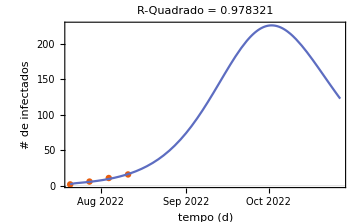

```mathematica
Quiet @ fitInfectedDynamic["ParameterTable"]
Quiet @ fitInfectedDynamic["BestFitParameters"]
Quiet @fitInfectedDynamic["RSquared"]
Quiet @fitInfectedDynamic["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamic,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

### Simulação 2

```mathematica
resultsS01 =Map[ParametricFunctionValues[#,<|β->0.224,α1->1.00,α2->0|>, {0,21,1}]&, asolDynamicBeta];
s01AsMap = Map[Last[Last[Last[#]]]&,Normal@resultsS01]
```

```mathematica
Total[Take[s01AsMap,5]]
```

```mathematica
AbsoluteTiming[fitInfectedDynamic02=NonlinearModelFit[s02,{infectedSolDynamic[t], {β >0 && α1 >0 &&  α2 >0}},{{β,0.224}, {α1,1.},{α2,0.001}},t, EvaluationMonitor:> Print["β=", β,"  .α1=",α1,"   .α2=",α2],Method-> {NMinimize, Method->{"NelderMead", "PostProcess"-> {"FindMinimum"}}}]]
```

β=0.224  .α1=1.   .α2=0.001

β=1.07973  .α1=1.66718   .α2=1.65312

β=0.627259  .α1=1.76191   .α2=0.841764

β=1.3341  .α1=0.655373   .α2=1.45509

β=1.1313  .α1=0.453123   .α2=1.23104

β=0.713206  .α1=0.042381   .α2=0.138303

β=0.044897  .α1=0.341629   .α2=0.0302618

β=0.0796861  .α1=0.46955   .α2=0.00943698

β=0.633031  .α1=0.666325   .α2=0.068898

β=0.19193  .α1=0.422803   .α2=0.0399208

β=0.673071  .α1=0.507239   .α2=0.110045

β=0.228032  .α1=0.478973   .α2=0.0345891

β=0.0361089  .α1=1.22547   .α2=0.00290346

β=0.46393  .α1=0.338153   .α2=0.0817363

β=0.226016  .α1=0.739486   .α2=0.0177945

β=0.470619  .α1=0.260677   .α2=0.0864459

β=0.228032  .α1=0.478973   .α2=0.0345891

β=0.209981  .α1=0.450888   .α2=0.0372549

β=0.0191028  .α1=0.852221   .α2=0.0294763

β=0.120223  .α1=0.704335   .α2=0.0296779

β=0.322464  .α1=0.408563   .α2=0.0300811

β=0.170783  .α1=0.630392   .α2=0.0297787

β=0.271903  .α1=0.482506   .α2=0.0299803

β=0.196063  .α1=0.59342   .α2=0.0298291

β=0.246623  .α1=0.519477   .α2=0.0299299

β=0.257133  .α1=0.707736   .α2=0.0176207

β=0.221769  .α1=0.5151   .α2=0.0323464

β=0.245345  .α1=0.643524   .α2=0.0225293

β=0.227663  .α1=0.547206   .α2=0.0298921

β=0.238836  .α1=0.725141   .α2=0.0171553

β=0.230733  .α1=0.540515   .α2=0.0302306

β=0.209652  .α1=0.69866   .α2=0.0220149

β=0.23738  .α1=0.564273   .α2=0.0279512

β=0.237835  .α1=0.361843   .α2=0.0409214

β=0.228971  .α1=0.645075   .α2=0.0235763

β=0.23706  .α1=0.619369   .α2=0.0246133

β=0.230012  .α1=0.565247   .α2=0.0285724

β=0.222431  .α1=0.602951   .α2=0.0269684

β=0.233643  .α1=0.573943   .α2=0.0277055

β=0.231018  .α1=0.648995   .α2=0.0230055

β=0.230804  .α1=0.567635   .α2=0.0284243

β=0.234002  .α1=0.492807   .α2=0.0328919

β=0.230229  .α1=0.607008   .α2=0.0259052

β=0.233105  .α1=0.600477   .α2=0.0261176

β=0.230786  .α1=0.574054   .α2=0.0279587

β=0.232301  .α1=0.602369   .α2=0.0259552

β=0.231178  .α1=0.576318   .α2=0.0278071

β=0.227819  .α1=0.597645   .α2=0.0267418

β=0.232187  .α1=0.579868   .α2=0.0274646

β=0.232539  .α1=0.546486   .α2=0.0295817

β=0.230806  .α1=0.591878   .α2=0.0268243

β=0.231996  .α1=0.591322   .α2=0.0267719

β=0.231088  .α1=0.578371   .α2=0.027662

β=0.229862  .α1=0.58451   .α2=0.0273977

β=0.231606  .α1=0.581029   .α2=0.0274478

β=0.231155  .α1=0.5912   .α2=0.0268157

β=0.231173  .α1=0.580039   .α2=0.0275592

β=0.231302  .α1=0.590259   .α2=0.0268922

β=0.231141  .α1=0.581343   .α2=0.0274696

β=0.231807  .α1=0.569729   .α2=0.0281601

β=0.231056  .α1=0.586341   .α2=0.0271583

β=0.230641  .α1=0.58412   .α2=0.0273435

β=0.231365  .α1=0.581801   .α2=0.0274218

β=0.231202  .α1=0.586285   .α2=0.0271405

β=0.23118  .α1=0.5816   .α2=0.0274545

β=0.231401  .α1=0.576823   .α2=0.027739

β=0.231143  .α1=0.583961   .α2=0.0273034

β=0.230945  .α1=0.582802   .α2=0.0273966

β=0.23126  .α1=0.582051   .α2=0.0274155

β=0.231247  .α1=0.583732   .α2=0.0273127

β=0.231168  .α1=0.58194   .α2=0.0274304

β=0.2312  .α1=0.583702   .α2=0.0273116

β=0.231185  .α1=0.582126   .α2=0.0274188

β=0.231071  .α1=0.5833   .α2=0.0273529

β=0.230976  .α1=0.583924   .α2=0.0273217

β=0.231035  .α1=0.584734   .α2=0.0272656

β=0.230968  .α1=0.58613   .α2=0.0271832

β=0.230917  .α1=0.586287   .α2=0.027175

β=0.230783  .α1=0.588368   .α2=0.0270531

β=0.23072  .α1=0.587389   .α2=0.0271234

β=0.230509  .α1=0.589103   .α2=0.0270334

β=0.230575  .α1=0.590879   .α2=0.0269131

β=0.23021  .α1=0.594166   .α2=0.0267341

β=0.229798  .α1=0.598882   .α2=0.0264684

β=0.229805  .α1=0.597542   .α2=0.0265569

β=0.229315  .α1=0.602129   .α2=0.0263088

β=0.229173  .α1=0.602531   .α2=0.026294

β=0.228349  .α1=0.613258   .α2=0.0256807

β=0.227269  .α1=0.625336   .α2=0.0250043

β=0.227374  .α1=0.621115   .α2=0.0252697

β=0.229192  .α1=0.60444   .α2=0.0261687

β=0.228011  .α1=0.618739   .α2=0.0253605

β=0.226999  .α1=0.630215   .α2=0.0247136

β=0.225841  .α1=0.644258   .α2=0.023916

β=0.224888  .α1=0.654448   .α2=0.0233519

β=0.223988  .α1=0.663955   .α2=0.0228209

β=0.224993  .α1=0.652651   .α2=0.0234558

β=0.223213  .α1=0.675569   .α2=0.0221448

β=0.224301  .α1=0.663532   .α2=0.0228193

β=0.223955  .α1=0.668972   .α2=0.022501

β=0.226577  .α1=0.636217   .α2=0.0243678

β=0.225736  .α1=0.646055   .α2=0.0238121

β=0.225466  .α1=0.651742   .α2=0.0234675

β=0.224264  .α1=0.666921   .α2=0.0226044

β=0.223475  .α1=0.678253   .α2=0.0219486

β=0.222862  .α1=0.68659   .α2=0.021466

β=0.221425  .α1=0.706858   .α2=0.020293

β=0.220438  .α1=0.717647   .α2=0.0196942

β=0.221695  .α1=0.701171   .α2=0.0206375

β=0.220442  .α1=0.721882   .α2=0.0194184

β=0.218685  .α1=0.748337   .α2=0.0178771

β=0.218899  .α1=0.741688   .α2=0.0182841

β=0.222331  .α1=0.694112   .α2=0.0210324

β=0.221104  .α1=0.714064   .α2=0.0198584

β=0.220808  .α1=0.72051   .α2=0.0194688

β=0.219452  .α1=0.738722   .α2=0.018421

β=0.218013  .α1=0.761027   .α2=0.0171153

β=0.219043  .α1=0.747218   .α2=0.0179124

β=0.217852  .α1=0.767398   .α2=0.0167221

β=0.2183  .α1=0.762538   .α2=0.0169896

β=0.217229  .α1=0.782866   .α2=0.0157751

β=0.215547  .α1=0.80548   .α2=0.0144767

β=0.219493  .α1=0.741753   .α2=0.0182208

β=0.216931  .α1=0.789289   .α2=0.015391

β=0.21567  .α1=0.814573   .α2=0.013876

β=0.214341  .α1=0.834806   .α2=0.0126947

β=0.213642  .α1=0.854098   .α2=0.0115084

β=0.211536  .α1=0.897448   .α2=0.00890161

β=0.216686  .α1=0.799552   .α2=0.014745

β=0.2161  .α1=0.808366   .α2=0.0142324

β=0.213045  .α1=0.868492   .α2=0.0106361

β=0.210953  .α1=0.911306   .α2=0.0080666

β=0.212138  .α1=0.883077   .α2=0.00978128

β=0.215109  .α1=0.827043   .α2=0.0131196

β=0.212194  .α1=0.885183   .α2=0.00963346

β=0.214801  .α1=0.832226   .α2=0.0128154

β=0.214996  .α1=0.831076   .α2=0.0128723

β=0.213452  .α1=0.860819   .α2=0.0110962

β=0.212623  .α1=0.877707   .α2=0.0100845

β=0.212537  .α1=0.876615   .α2=0.0101595

β=0.214381  .α1=0.842461   .α2=0.0121941

β=0.212451  .α1=0.882289   .α2=0.00980224

β=0.21381  .α1=0.855221   .α2=0.0114256

β=0.214193  .α1=0.848585   .α2=0.0118203

β=0.212094  .α1=0.889759   .α2=0.00935526

β=0.213809  .α1=0.854285   .α2=0.0114844

β=0.21493  .α1=0.831261   .α2=0.0128685

β=0.213071  .α1=0.869532   .α2=0.0105688

β=0.213675  .α1=0.85854   .α2=0.011223

β=0.213787  .α1=0.8574   .α2=0.0112864

β=0.213228  .α1=0.86791   .α2=0.0106605

β=0.212937  .α1=0.874722   .α2=0.0102486

β=0.212645  .α1=0.879975   .α2=0.00993469

β=0.213101  .α1=0.872626   .α2=0.0103687

β=0.213116  .α1=0.874173   .α2=0.0102687

β=0.212114  .α1=0.893009   .α2=0.00914503

β=0.211334  .α1=0.910244   .α2=0.00810605

β=0.21279  .α1=0.880263   .α2=0.00990688

β=0.212863  .α1=0.880406   .α2=0.00989297

β=0.212399  .α1=0.889209   .α2=0.00936513

β=0.21213  .α1=0.896453   .α2=0.00892339

β=0.211588  .α1=0.907191   .α2=0.00828149

β=0.212225  .α1=0.896262   .α2=0.00892947

β=0.211172  .α1=0.919675   .α2=0.00751602

β=0.210364  .α1=0.939381   .α2=0.00632059

β=0.210497  .α1=0.932421   .α2=0.00675417

β=0.211793  .α1=0.905302   .α2=0.00838565

β=0.211269  .α1=0.920233   .α2=0.0074716

β=0.21111  .α1=0.926754   .α2=0.00706665

β=0.210154  .α1=0.946824   .α2=0.00586184

β=0.209166  .α1=0.972009   .α2=0.00433106

β=0.209398  .α1=0.965657   .α2=0.00471704

β=0.210184  .α1=0.949095   .α2=0.00571306

β=0.210094  .α1=0.953952   .α2=0.00540929

β=0.208555  .α1=0.987484   .α2=0.00338969

β=0.210591  .α1=0.937046   .α2=0.00645112

β=0.211221  .α1=0.922987   .α2=0.00730031

β=0.209854  .α1=0.954989   .α2=0.00536285

β=0.210265  .α1=0.947263   .α2=0.00582285

β=0.209611  .α1=0.963852   .α2=0.00481472

β=0.209122  .α1=0.977255   .α2=0.00399652

β=0.20986  .α1=0.960753   .α2=0.0049921

β=0.209179  .α1=0.977473   .α2=0.00397826

β=0.208635  .α1=0.992578   .α2=0.00305597

β=0.208227  .α1=1.00463   .α2=0.00231667

β=0.207249  .α1=1.0324   .α2=0.000618474

β=0.207463  .α1=1.02222   .α2=0.00125401

β=0.209261  .α1=0.97612   .α2=0.00405757

β=0.208227  .α1=1.00463   .α2=0.00231667

β=0.208227  .α1=1.00463   .α2=0.00231667

β=0.208227  .α1=1.00463   .α2=0.00231667

β=0.208227  .α1=1.00463   .α2=0.00231668

β=0.208227  .α1=1.00463   .α2=0.00231667

β=0.208227  .α1=1.00463   .α2=0.00231667

β=0.208227  .α1=1.00463   .α2=0.00231667

«2 more identical outputs»

β=0.208227  .α1=1.00463   .α2=0.00231668

β=0.208227  .α1=1.00463   .α2=0.00231667

β=0.709744  .α1=1.01547   .α2=-0.105035

β=0.709744  .α1=1.01547   .α2=-0.105035

β=0.709744  .α1=1.01547   .α2=-0.105035

«2 more identical outputs»

β=0.208241  .α1=1.00463   .α2=0.00231368

β=0.208241  .α1=1.00463   .α2=0.00231368

β=0.208241  .α1=1.00463   .α2=0.00231368

β=0.208241  .α1=1.00463   .α2=0.00231369

β=0.208241  .α1=1.00463   .α2=0.00231368

β=0.208341  .α1=1.00463   .α2=0.00229142

β=0.208341  .α1=1.00463   .α2=0.00229142

β=0.208341  .α1=1.00463   .α2=0.00229142

β=0.208341  .α1=1.00463   .α2=0.00229143

β=0.208341  .α1=1.00463   .α2=0.00229142

β=0.208341  .α1=1.00463   .α2=0.00229068

β=0.208341  .α1=1.00463   .α2=0.00229068

β=0.208341  .α1=1.00463   .α2=0.00229068

β=0.208341  .α1=1.00463   .α2=0.00229069

β=0.208341  .α1=1.00463   .α2=0.00229068

β=0.208337  .α1=1.00464   .α2=0.0022833

β=0.208337  .α1=1.00464   .α2=0.0022833

β=0.208337  .α1=1.00464   .α2=0.0022833

β=0.208337  .α1=1.00464   .α2=0.00228332

β=0.208337  .α1=1.00464   .α2=0.0022833

β=0.208331  .α1=1.00464   .α2=0.00226439

β=0.208331  .α1=1.00464   .α2=0.00226439

β=0.208331  .α1=1.00464   .α2=0.00226439

β=0.208331  .α1=1.00464   .α2=0.0022644

β=0.208331  .α1=1.00464   .α2=0.00226439

β=0.208313  .α1=1.00467   .α2=0.00220313

β=0.208313  .α1=1.00467   .α2=0.00220313

β=0.208313  .α1=1.00467   .α2=0.00220313

β=0.208313  .α1=1.00467   .α2=0.00220315

β=0.208313  .α1=1.00467   .α2=0.00220313

β=0.208271  .α1=1.00474   .α2=0.00203856

β=0.208271  .α1=1.00474   .α2=0.00203856

β=0.208271  .α1=1.00474   .α2=0.00203856

β=0.208271  .α1=1.00474   .α2=0.00203858

β=0.208271  .α1=1.00474   .α2=0.00203856

β=0.208164  .α1=1.00493   .α2=0.00158643

β=0.208164  .α1=1.00493   .α2=0.00158643

β=0.208164  .α1=1.00493   .α2=0.00158643

β=0.208164  .α1=1.00493   .α2=0.00158644

β=0.208164  .α1=1.00493   .α2=0.00158643

β=0.207892  .α1=1.00542   .α2=0.000399444

β=0.207892  .α1=1.00542   .α2=0.000399444

β=0.207892  .α1=1.00542   .α2=0.000399444

β=0.207892  .α1=1.00542   .α2=0.000399459

β=0.207892  .α1=1.00542   .α2=0.000399444

β=0.207226  .α1=1.00668   .α2=-0.00259151

β=0.207226  .α1=1.00668   .α2=-0.00259151

β=0.207226  .α1=1.00668   .α2=-0.00259151

β=0.207226  .α1=1.00668   .α2=-0.00259149

β=0.207226  .α1=1.00668   .α2=-0.00259151

β=0.205924  .α1=1.00917   .α2=-0.00856192

β=0.205924  .α1=1.00917   .α2=-0.00856192

β=0.205924  .α1=1.00917   .α2=-0.00856192

β=0.205924  .α1=1.00917   .α2=-0.00856191

β=0.205924  .α1=1.00917   .α2=-0.00856192

β=0.203755  .α1=1.0134   .α2=-0.0186815

β=0.203755  .α1=1.0134   .α2=-0.0186815

β=0.203755  .α1=1.0134   .α2=-0.0186815

«2 more identical outputs»

β=0.20099  .α1=1.0189   .α2=-0.0318724

β=0.20099  .α1=1.0189   .α2=-0.0318724

β=0.20099  .α1=1.0189   .α2=-0.0318724

«2 more identical outputs»

β=0.197425  .α1=1.02621   .α2=-0.0493981

β=0.197425  .α1=1.02621   .α2=-0.0493981

β=0.197425  .α1=1.02621   .α2=-0.0493981

«2 more identical outputs»

β=0.194318  .α1=1.03268   .α2=-0.0649383

β=0.194318  .α1=1.03268   .α2=-0.0649383

β=0.194318  .α1=1.03268   .α2=-0.0649383

«2 more identical outputs»

β=0.188519  .α1=1.04456   .α2=-0.0934422

β=0.188519  .α1=1.04456   .α2=-0.0934422

β=0.188519  .α1=1.04456   .α2=-0.0934422

«2 more identical outputs»

β=0.192085  .α1=1.03725   .α2=-0.0759155

β=0.192085  .α1=1.03725   .α2=-0.0759155

β=0.192085  .α1=1.03725   .α2=-0.0759155

«2 more identical outputs»

β=0.187672  .α1=1.04652   .α2=-0.0981781

β=0.187672  .α1=1.04652   .α2=-0.0981781

β=0.187672  .α1=1.04652   .α2=-0.0981781

«2 more identical outputs»

β=0.186872  .α1=1.04836   .α2=-0.102604

β=0.186872  .α1=1.04836   .α2=-0.102604

β=0.186872  .α1=1.04836   .α2=-0.102604

«2 more identical outputs»

β=0.184626  .α1=1.05307   .α2=-0.11393

β=0.184626  .α1=1.05307   .α2=-0.11393

β=0.184626  .α1=1.05307   .α2=-0.11393

«2 more identical outputs»

β=0.184411  .α1=1.05355   .α2=-0.115079

β=0.184411  .α1=1.05355   .α2=-0.115079

β=0.184411  .α1=1.05355   .α2=-0.115079

«2 more identical outputs»

β=0.183778  .α1=1.05492   .α2=-0.118364

β=0.183778  .α1=1.05492   .α2=-0.118364

β=0.183778  .α1=1.05492   .α2=-0.118364

«2 more identical outputs»

β=0.183834  .α1=1.0548   .α2=-0.118088

β=0.183834  .α1=1.0548   .α2=-0.118088

β=0.183834  .α1=1.0548   .α2=-0.118088

«2 more identical outputs»

β=0.18381  .α1=1.05485   .α2=-0.118207

β=0.18381  .α1=1.05485   .α2=-0.118207

β=0.18381  .α1=1.05485   .α2=-0.118207

«2 more identical outputs»

β=0.183809  .α1=1.05485   .α2=-0.118215

β=0.183809  .α1=1.05485   .α2=-0.118215

β=0.183809  .α1=1.05485   .α2=-0.118215

«2 more identical outputs»

β=0.18381  .α1=1.05485   .α2=-0.118207

β=0.18381  .α1=1.05485   .α2=-0.118207

β=0.18381  .α1=1.05485   .α2=-0.118207

«97 more identical outputs»

β=0.18381  .α1=1.05485   .α2=0.

β=0.208227  .α1=1.00463   .α2=0.00231667

β=0.18381  .α1=1.05485   .α2=0.

β=0.18381  .α1=1.05485   .α2=0.

β=0.18381  .α1=1.05485   .α2=0.

β=0.18381  .α1=1.05485   .α2=1.49012×10^-8

β=0.18381  .α1=1.05485   .α2=0.

β=0.71083  .α1=1.06115   .α2=-0.0939888

β=0.71083  .α1=1.06115   .α2=-0.0939888

β=0.71083  .α1=1.06115   .α2=-0.0939888

β=0.71083  .α1=1.06115   .α2=-0.0939887

β=0.71083  .α1=1.06115   .α2=-0.0939888

β=0.185058  .α1=1.05486   .α2=-0.000222554

β=0.185058  .α1=1.05486   .α2=-0.000222554

β=0.185058  .α1=1.05486   .α2=-0.000222554

β=0.185058  .α1=1.05486   .α2=-0.000222539

β=0.185058  .α1=1.05486   .α2=-0.000222554

β=0.212999  .α1=1.0552   .α2=-0.00520558

β=0.212999  .α1=1.0552   .α2=-0.00520558

β=0.212999  .α1=1.0552   .α2=-0.00520558

β=0.212999  .α1=1.0552   .α2=-0.00520557

β=0.212999  .α1=1.0552   .α2=-0.00520558

β=0.199121  .α1=1.05503   .α2=-0.00273045

β=0.199121  .α1=1.05503   .α2=-0.00273045

β=0.199121  .α1=1.05503   .α2=-0.00273045

β=0.199121  .α1=1.05503   .α2=-0.00273044

β=0.199121  .α1=1.05503   .α2=-0.00273045

β=0.221166  .α1=1.05543   .α2=-0.0073362

β=0.221166  .α1=1.05543   .α2=-0.0073362

β=0.221166  .α1=1.05543   .α2=-0.0073362

β=0.221166  .α1=1.05543   .α2=-0.00733619

β=0.221166  .α1=1.05543   .α2=-0.0073362

β=0.205261  .α1=1.05514   .α2=-0.00401323

β=0.205261  .α1=1.05514   .α2=-0.00401323

β=0.205261  .α1=1.05514   .α2=-0.00401323

β=0.205261  .α1=1.05514   .α2=-0.00401321

β=0.205261  .α1=1.05514   .α2=-0.00401323

β=0.206478  .α1=1.05517   .α2=-0.00429252

β=0.206478  .α1=1.05517   .α2=-0.00429252

β=0.206478  .α1=1.05517   .α2=-0.00429252

β=0.206478  .α1=1.05517   .α2=-0.00429251

β=0.206478  .α1=1.05517   .α2=-0.00429252

β=0.206159  .α1=1.05516   .α2=-0.00422109

β=0.206159  .α1=1.05516   .α2=-0.00422109

β=0.206159  .α1=1.05516   .α2=-0.00422109

β=0.206159  .α1=1.05516   .α2=-0.00422107

β=0.206159  .α1=1.05516   .α2=-0.00422109

β=0.20617  .α1=1.05517   .α2=-0.00422624

β=0.20617  .α1=1.05517   .α2=-0.00422624

β=0.20617  .α1=1.05517   .α2=-0.00422624

β=0.20617  .α1=1.05517   .α2=-0.00422622

β=0.20617  .α1=1.05517   .α2=-0.00422624

β=0.206169  .α1=1.05517   .α2=-0.00422905

β=0.206169  .α1=1.05517   .α2=-0.00422905

β=0.206169  .α1=1.05517   .α2=-0.00422905

β=0.206169  .α1=1.05517   .α2=-0.00422904

β=0.206169  .α1=1.05517   .α2=-0.00422905

$Aborted

```mathematica
Quiet @ fitInfectedDynamic02["ParameterTable"]
Quiet @ fitInfectedDynamic02["BestFitParameters"]
Quiet @fitInfectedDynamic02["RSquared"]
Quiet @fitInfectedDynamic02["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamic02,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

fitInfectedDynamic02[ParameterTable]

fitInfectedDynamic02[BestFitParameters]

fitInfectedDynamic02[RSquared]

fitInfectedDynamic02[AdjustedRSquared]

FitWithDataPlot[fitInfectedDynamic02,{Thu 21 Jul 2022 00:00:00GMT-3,Thu 27 Oct 2022 00:00:00GMT-3}]

```mathematica
Association@Quiet @ fitInfectedDynamic02["BestFitParameters"]
```

### Simulação 3

```mathematica
AbsoluteTiming[fitInfectedDynamic03=NonlinearModelFit[s03,{infectedSolDynamic[t], {0<β && 0<α1<=1 && 0< α2<=1}},{{β,0.217}, {α1,0.803},{α2,0.0170}},t, AccuracyGoal-> 3, WorkingPrecision-> 3,  PrecisionGoal -> 3, EvaluationMonitor:> Print["β=", β,"  .α1=",α1,"   .α2=",α2],Method-> {NMinimize, Method->{"NelderMead", "PostProcess"-> {"FindMinimum"}}}]]
```

```mathematica
Quiet @ fitInfectedDynamic03["ParameterTable"]
Quiet @ fitInfectedDynamic03["BestFitParameters"]
Quiet @fitInfectedDynamic03["RSquared"]
Quiet @fitInfectedDynamic03["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamic03,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

### Simulação 4

```mathematica
AbsoluteTiming[fitInfectedDynamic04=NonlinearModelFit[s04,{infectedSolDynamic[t], {0<β && 0<α1<=1 && 0< α2<=1}},{{β,0.356}, {α1,0.999},{α2,0.686}},t, AccuracyGoal-> 3, WorkingPrecision-> 3,  PrecisionGoal -> 3, EvaluationMonitor:> Print["β=", β,"  .α1=",α1,"   .α2=",α2],Method-> {NMinimize, Method->{"NelderMead", "PostProcess"-> {"FindMinimum"}}}]]
```

```mathematica
Quiet @ fitInfectedDynamic04["ParameterTable"]
Quiet @ fitInfectedDynamic04["BestFitParameters"]
Quiet @fitInfectedDynamic04["RSquared"]
Quiet @fitInfectedDynamic04["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamic04,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

### Simulação 5

```mathematica
AbsoluteTiming[fitInfectedDynamic05=NonlinearModelFit[s05,{infectedSolDynamic[t], {0<β && 0<α1<=1 && 0< α2<=1}},{{β,0.354}, {α1,0.377},{α2,0.216}},t, AccuracyGoal-> 3, WorkingPrecision-> 3,  PrecisionGoal -> 3, EvaluationMonitor:> Print["β=", β,"  .α1=",α1,"   .α2=",α2],Method-> {NMinimize, Method->{"NelderMead", "PostProcess"-> {"FindMinimum"}}}]]
```

```mathematica
Quiet @ fitInfectedDynamic05["ParameterTable"]
Quiet @ fitInfectedDynamic05["BestFitParameters"]
Quiet @fitInfectedDynamic05["RSquared"]
Quiet @fitInfectedDynamic05["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamic05,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

### Simulação Total

```mathematica
AbsoluteTiming[fitInfectedDynamicAll=NonlinearModelFit[all,{infectedSolDynamic[t], {β > 0 && 0<α1<=1  && 0<α2<=1}},{{β,0.517}, {α1,0.729},{α2,0.692}},t,Method-> {NMinimize, Method->{"NelderMead"}}]]
```

$Aborted

```mathematica
Quiet @ fitInfectedDynamicAll["ParameterTable"]
Quiet @ fitInfectedDynamicAll["BestFitParameters"]
Quiet @fitInfectedDynamicAll["RSquared"]
Quiet @fitInfectedDynamicAll["AdjustedRSquared"]
Quiet @FitWithDataPlot[fitInfectedDynamicAll,{First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]} ]
```

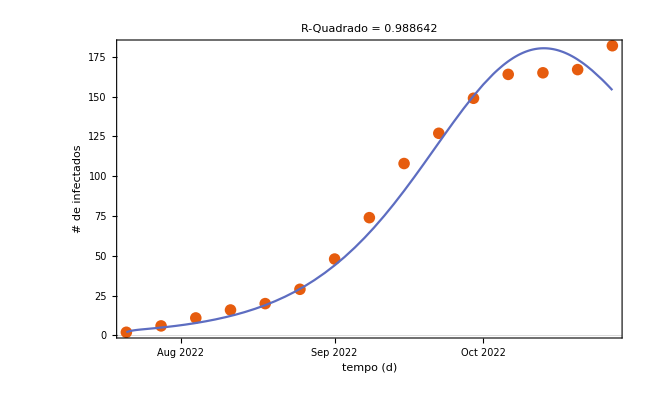

```mathematica
00001.260604874863131`3*10^-4
```

```mathematica
RealDigits[0.0001260604874863131`3.]
```

```mathematica
Chunk[list_,chunk_]:=Flatten[Partition[list,chunk][[#;;;;2]]]&/@{1,2}
```

```mathematica
fits ={fitInfectedDynamic, fitInfectedDynamic02, fitInfectedDynamic03, fitInfectedDynamic04, fitInfectedDynamic05}
```

```mathematica
JoinFittedDatePlot[fits_List,fitComplete_FittedModel,{dateMin_DateObject,dateMax_DateObject}]:=
Module[{plotAll,plotData,bands,cd, chunks},
cd=ColorData[108];
firstFit = First@fits;
lastFit = Last@fits;
plotAll={ToDataDate[dateMin,#1],#2}&@@@fitComplete["Data"];
plotData=Map[{ToDataDate[dateMin,#1],#2}&@@@#["Data"]&,fits];
bands[x_]=Quiet @ fitComplete["SinglePredictionBands",ConfidenceLevel->0.95]&/. t->x;
Show[DateListPlot[plotAll,Joined->True,PlotRange->All],
DateListPlot[plotData,Joined->False,PlotRange->All,PlotTheme->"Detailed"],
Plot[{fitComplete[ToModelTime[dateMin,FromAbsoluteTime@t]]&,
bands[ToModelTime[dateMin,FromAbsoluteTime@t]]},
{t,AbsoluteTime@dateMin,AbsoluteTime@dateMax},
PlotRange->All,
PlotStyle->{cd[2],None},
Filling->{2->{1}},
FillingStyle->{Opacity[0.5,Lighter@cd[2]]},
Exclusions->None],
PlotRange->All,
PlotRangePadding->{Automatic,{Scaled[0.03],Scaled[0.1]}},
FrameLabel->{"tempo (d)","# de infectados"},ImageSize->360,
PlotLabel->StringForm["Simulações com parâmetros ajustados"]]
//Labeled[#,Column[{LineLegend[{cd[1]},{"S00"}],PointLegend[{cd[2]},{"S01"}],PointLegend[{cd[3]},{"S02"}],PointLegend[{cd[4]},{"S03"}],PointLegend[{cd[5]},{"S04"}], PointLegend[{cd[6]},{"S05"}]},Left],Right]&]
```

```mathematica
JoinFittedDatePlot[fits,fitInfectedDynamicAll, {First@First@Normal[currentDynamic],First@Last@Normal[currentDynamic]}]
```

```mathematica
dateMin = First@First@Normal[currentDynamic];
dateMax = First@Last@Normal[currentDynamic];
bands[x_,t_]=Quiet @ Map[#["SinglePredictionBands",ConfidenceLevel->0.95]&/. t->x, fits]
```

## Modelo Final

```mathematica
(*lastFit = fitInfectedDynamic05 ;
lastParameters = Association@fitInfectedDynamic04["BestFitParameters"]*)
(*Normal@lastParameters[[2]]*)
(*lastFit["Data"]*)
lastParameters=<|β->0.332, α1->0.160, α2->0.053|>
resultsLastSimulation =Map[ParametricFunctionValues[#,<|β->0.332, α1->0.160, α2->0.053|>, {84,98,1}]&, asolDynamicBeta]
resultsLastSimulationMap = Map[Last[Last[Last[#]]]&,Normal@resultsLastSimulation]
```

<|β→0.332,α1→0.16,α2→0.053|>

<|SP→{{84,1454.66},{85,1426.53},{86,1398.52},{87,1370.7},{88,1343.1},{89,1315.78},{90,1288.8},{91,1262.19},{92,1236.01},{93,1210.28},{94,1185.05},{95,1160.35},{96,1136.2},{97,1112.64},{98,1089.68}},EP→{{84,148.041},{85,149.128},{86,149.944},{87,150.483},{88,150.744},{89,150.727},{90,150.433},{91,149.865},{92,149.031},{93,147.938},{94,146.596},{95,145.015},{96,143.208},{97,141.188},{98,138.971}},IP→{{84,159.785},{85,162.751},{86,165.5},{87,168.018},{88,170.291},{89,172.307},{90,174.054},{91,175.525},{92,176.712},{93,177.611},{94,178.217},{95,178.53},{96,178.55},{97,178.28},{98,177.724}},QP→{{84,22.908},{85,23.198},{86,23.4493},{87,23.6604},{88,23.8301},{89,23.9573},{90,24.0415},{91,24.0823},{92,24.0796},{93,24.0338},{94,23.9455},{95,23.8156},{96,23.6453},{97,23.436},{98,23.1894}},RP→{{84,582.606},{85,606.392},{86,630.582},{87,655.142},{88,680.035},{89,705.225},{90,730.671},{91,756.333},{92,782.168},{93,808.136},{94,834.191},{95,860.292},{96,886.395},{97,912.457},{98,938.437}}|>

{1089.68,138.971,177.724,23.1894,938.437}

```mathematica
modelSEIQRFinal = SetRateRules[modelSEIQRDynamicBeta, <|
NP[0] -> Total[resultsLastSimulationMap],  
β->Normal@lastParameters[[1]],
α1-> Normal@lastParameters[[2]],
α2->Normal@lastParameters[[3]]|>];
modelSEIQRFinal["InitialConditions"] = ReplacePart[modelSEIQRFinal["InitialConditions"], 3->IP[0]== resultsLastSimulationMap[[3]]]
modelSEIQRFinal = SetInitialConditions[modelSEIQRFinal,
   <|
SP[0] -> resultsLastSimulationMap[[1]],
EP[0] -> resultsLastSimulationMap[[2]],
IP[t ;/ t<=0] -> resultsLastSimulationMap[[3]],
QP[0] -> resultsLastSimulationMap[[4]],
RP[0] -> resultsLastSimulationMap[[5]]
    |>]; 

lsActualEquationsFinal = Join[modelSEIQRFinal["Equations"] //. KeyDrop[modelSEIQRFinal["RateRules"], {}], modelSEIQRFinal["InitialConditions"]]
modelSEIQRFinal["InitialConditions"]
ModelGridTableForm[modelSEIQRFinal]
ResourceFunction["GridTableForm"][List /@ lsActualEquationsFinal]
aSolFinal = NDSolve[lsActualEquationsFinal,{SP,EP,IP,QP, RP},{t,0,60}]
```

{SP[0]==2356,EP[0]==2,IP[0]==177.724,QP[0]==8,RP[0]==0}

{SP'[t]==0.2 QP[t]-0.000140203 IP[t] SP[t],EP'[t]==-0.213 EP[t]+0.000140203 IP[t] SP[t],IP'[t]==0.16 EP[t]-(4 IP[t])/31,QP'[t]==0.053 EP[t]-0.329032 QP[t],RP'[t]==(4 IP[t])/31+(4 QP[t])/31,SP[0]==1089.68,EP[0]==138.971,IP[0]==177.724,QP[0]==23.1894,RP[0]==938.437}

{SP[0]==1089.68,EP[0]==138.971,IP[0]==177.724,QP[0]==23.1894,RP[0]==938.437}

<|Stocks→# | Symbol | Description
1 | NP[t] | Total Population
2 | SP[t] | Susceptible Population
3 | EP[t] | Exposed Population
4 | IP[t] | Infected Population
5 | QP[t] | Quarantined Population
6 | RP[t] | Recovered Population,Rates→# | Symbol | Description
1 | β | Contact rate for the infected population
2 | α1 | Proportion of Exposed to Infected Rate (Confirmed)
3 | α2 | Proportion Sent to Quarantine (Suspected)
4 | φ | Proportion of not detected after medical diagnosis (Discarded)
5 | τ | Proportion from Suspected to Recovered class
6 | γ | Recovery Rate
7 | ζ | Average Incubation Period
8 | λ | Average Infection Period,Equations→# | Equation
1 | SP'[t]==φ QP[t]-(β IP[t] SP[t])/NP[0]
2 | EP'[t]==-((α1+α2) EP[t])+(β IP[t] SP[t])/NP[0]
3 | IP'[t]==α1 EP[t]-γ IP[t]
4 | QP'[t]==α2 EP[t]-(τ+φ) QP[t]
5 | RP'[t]==γ IP[t]+τ QP[t],RateRules→# | Symbol | Value
1 | NP[0] | 2368.
2 | β | 0.332
3 | α1 | 0.16
4 | α2 | 0.053
5 | φ | 0.2
6 | τ | γ
7 | γ | 1/λ
8 | ζ | 13
9 | λ | 31/4,InitialConditions→# | Equation
1 | SP[0]==1089.68
2 | EP[0]==138.971
3 | IP[0]==177.724
4 | QP[0]==23.1894
5 | RP[0]==938.437|>

# | 1
1 | SP'[t]==0.2 QP[t]-0.000140203 IP[t] SP[t]
2 | EP'[t]==-0.213 EP[t]+0.000140203 IP[t] SP[t]
3 | IP'[t]==0.16 EP[t]-(4 IP[t])/31
4 | QP'[t]==0.053 EP[t]-0.329032 QP[t]
5 | RP'[t]==(4 IP[t])/31+(4 QP[t])/31
6 | SP[0]==1089.68
7 | EP[0]==138.971
8 | IP[0]==177.724
9 | QP[0]==23.1894
10 | RP[0]==938.437

{{SP→InterpolatingFunction[…],EP→InterpolatingFunction[…],IP→InterpolatingFunction[…],QP→InterpolatingFunction[…],RP→InterpolatingFunction[…]}}

```mathematica
aSolForPeaks = Association@Flatten@ParametricNDSolve[lsActualEquationsFinal,{SP,EP,IP,QP, RP},{t,0,60},{β,α1,α2}]
```

<|SP→ParametricFunction[<>],EP→ParametricFunction[<>],IP→ParametricFunction[<>],QP→ParametricFunction[<>],RP→ParametricFunction[<>]|>

```mathematica
allValues =Map[ParametricFunctionValues[#,lastParameters, {0,60,1}]&, aSolForPeaks];
peaks = Map[FindPeaks[Last/@#]&,allValues]
```

<|SP→{{1,1089.68}},EP→{{1,138.971}},IP→{{1,177.724}},QP→{{1,23.1894}},RP→{{61,1751.16}}|>

```mathematica
Clear[PadRealData];
PadRealData[aData:Association[(_String->_?VectorQ)..],incubationPeriod_?IntegerQ,infectiousPeriod_?IntegerQ]:=Block[{},Join[ConstantArray[0,incubationPeriod+infectiousPeriod],#]&/@aData];
```

```mathematica
optsFinal={PlotRange->All,PlotLegends->None,PlotTheme->"Detailed",PerformanceGoal->"Speed",ImageSize->800};
DynamicModule[{beta=Normal@lastParameters[[1]],alpha1=Normal@lastParameters[[2]],alpha2=Normal@lastParameters[[3]],nWeeks=60},
DynamicModule[{modelSEIQR=modelSEIQRFinal,lsFinal},
lsFinal = ParametricSolutionsPlots[modelSEIQR["Stocks"],#,None,nWeeks,"Together"->True,optsFinal]&/@GroupBy[Normal@aSolFinal,#[[1,1]]&,Association];
(*Show[List@Plot[Map[Identity[#]&,Values[aSolFinal]],{t,0,100}, PlotRange->All,PlotLegends->None,PlotTheme->"Detailed"], ListPlot[peaks,PlotStyle-> {Red,Black,Blue}]]]]*)
Show[lsFinal[[1,1]],ListPlot[Labeled[#,#]&/@peaks, PlotLabels->Above,PlotLegends->None]]
]
]
```

```mathematica
GroupBy[Normal@aSolFinal,#[[1,1]]&,Association]
```

<|SP→<|SP→InterpolatingFunction[…],EP→InterpolatingFunction[…],IP→InterpolatingFunction[…],QP→InterpolatingFunction[…],RP→InterpolatingFunction[…]|>|>

```mathematica
ParametricSolutionsPlots[modelSEIQRFinal["Stocks"],Normal@aSolFinal,{0.332,0.160,0.053},160,"Together"->True,optsFinal]
```

ParametricSolutionsPlots[<|NP[t]→Total Population,SP[t]→Susceptible Population,EP[t]→Exposed Population,IP[t]→Infected Population,QP[t]→Quarantined Population,RP[t]→Recovered Population|>,{{SP→InterpolatingFunction[…],EP→InterpolatingFunction[…],IP→InterpolatingFunction[…],QP→InterpolatingFunction[…],RP→InterpolatingFunction[…]}},{0.332,0.16,0.053},160,Together→True,{PlotRange→All,PlotLegends→None,PlotTheme→Detailed,PerformanceGoal→Speed,ImageSize→800}]

```mathematica
lsFinal = ParametricSolutionsPlots[modelSEIQRFinal["Stocks"],#,{{β,0.332},{α1,0.16},{α2,0.053}},160,"Together"->True,optsFinal]&/@GroupBy[Normal@aSolFinal,#[[1,1]]&,Association]
```

<|SP→{-Graphics-}|>

## Sensibilidade de parâmetro

```mathematica
ResidualsPlot[fitInfectedDynamic05]
```

ResidualsPlot[fitInfectedDynamic05]

```mathematica
ClearAll[modelSensitivityPlot]
modelSensitivityPlot[modelIn:(_ParametricFunction[__]),fit_FittedModel,{{tMin_?NumberQ,tMax_?NumberQ},{yMin_?NumberQ,yMax_?NumberQ}},scale:{__?NumberQ}]:=Module[{model,sensitivities,cd=ColorData[108],params,t},params=fit["BestFitParameters"];
model=modelIn[t]/. params;
sensitivities=MapThread[model+(#2 {-1,1} D[modelIn,#1][t]/. params)&,{Keys@params,scale}];
TabView@MapThread[Function[{p,bands,sf},p->(Show[ListPlot[fit["Data"],PlotRange->All],Plot[{model,bands}//Evaluate,{t,tMin,tMax},PlotRange->All,PlotStyle->{cd[2],Lighter@cd[3],Lighter@cd[4]},Filling->{2->{{1},Opacity[0.5,Lighter@cd[3]]},3->{{1},Opacity[0.5,Lighter@cd[4]]}}],PlotRange->{All,{yMin,yMax}},PlotRangePadding->{Automatic,{Scaled[0.03],Scaled[0.1]}},FrameLabel->{"tempo (t) dias","# de infectados"},PlotLabel->"Sensibilidade do parâmetro",Epilog->{Inset[StringForm["Fator de Escala = ``",TraditionalForm[sf]],Scaled[{0.05,0.95}],{-1,1}]}]//Labeled[#,Column[{PointLegend[{cd[1]},{"Observado"}],LineLegend[{cd[2]},{"Calculado"}],SwatchLegend[{Opacity[0.5,Lighter@cd[3]]},{"Sensibilidade Negativa"}],SwatchLegend[{Opacity[0.5,Lighter@cd[4]]},{"Sensibilidade Positiva"}]},Left],Right]&)],{Keys@params,sensitivities,scale}]]
```

```mathematica
modelSensitivityPlot[infectedSolDynamic,fitInfectedDynamic05,{{0,100},{-10,190}},{0.354, 0.377,0.216}]
```